```mathematica
(* WALKING KINEMATICS: PELVIC VECTOR ANGLE ANALYSIS PLOTS - Filtered, Archive data*)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(*This code requires the data outputs from WALKING KINEMATICS: STICK FIGURE PLUS 3D JOINT ANGLES.nb and WALKING KINEMATICS: STICK FIGURE PLUS PELVIC VECTOR ANGLE ANALYSIS.nb. This code looks at all trials simultaneously *)
```

```mathematica
(***********************************************************************************)
(***********************************************************************************)
```

```mathematica
(* Determine operating system *)

os=$OperatingSystem;
frogworkpath="C:\\YOUR FILE DIRECTORY HERE\\" (*Set your main file directory, not to the folder where raw or archived data are stored*)
(*e.g. frogworkpath="C:\\Users\\Documents\\"*)
(*for Mac users change "C:\\" to "\\Volumes\\"*)

(***********************************************************************************)

(* Import metadata*)
(*Set the directory where the METADATA.xlsx is saved*)

(*SET DIRECTORY*)
dataDirectory="YOUR DIRECTORY TO METADATA.xlsx FILE";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

importedmetadata=Import["METADATA.xlsx","Data"];
metadata=importedmetadata[[1,2;;24,All]];

(***********************************************************************************)

(* Metadata file map: Locate information *)

Framerate=metadata[[1,3]];


(***********************************************************************************)

dataDirectory="YOUR DIRECTORY FOR EXPORTED PELVIC VECTOR ANGLE DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData]

(*IMPORT PELVIC ANGLE DATA*)

Animal0Trial1data=Import["KM01_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial1data=Import["KM02_RUN_01_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial2data=Import["KM02_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal1Trial3data=Import["KM02_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial1data=Import["KM04_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial2data=Import["KM04_RUN_11_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal2Trial3data=Import["KM04_RUN_12_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial1data=Import["KM05_RUN_04_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal3Trial2data=Import["KM05_RUN_08_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial1data=Import["KM06_RUN_11_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial2data=Import["KM06_RUN_12_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial3data=Import["KM06_RUN_13_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial4data=Import["KM06_RUN_15_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal4Trial5data=Import["KM06_RUN_16_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial1data=Import["KM07_RUN_14_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial2data=Import["KM07_RUN_16_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal5Trial3data=Import["KM07_RUN_17_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial1data=Import["KM08_RUN_09_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal6Trial2data=Import["KM08_RUN_10_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial1data=Import["KM23_RUN_01_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial2data=Import["KM23_RUN_02_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial3data=Import["KM23_RUN_03_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];
Animal7Trial4data=Import["KM23_RUN_05_Pelvic Vector Angle Data - One Limb Cycle - FILTERED.xlsx","Data"];

Animal0Trial1=Flatten[Animal0Trial1data[[1]]];
Animal1Trial1=Flatten[Animal1Trial1data[[1]]];
Animal1Trial2=Flatten[Animal1Trial2data[[1]]];
Animal1Trial3=Flatten[Animal1Trial3data[[1]]];
Animal2Trial1=Flatten[Animal2Trial1data[[1]]];
Animal2Trial2=Flatten[Animal2Trial2data[[1]]];
Animal2Trial3=Flatten[Animal2Trial3data[[1]]];
Animal3Trial1=Flatten[Animal3Trial1data[[1]]];
Animal3Trial2=Flatten[Animal3Trial2data[[1]]];
Animal4Trial1=Flatten[Animal4Trial1data[[1]]];
Animal4Trial2=Flatten[Animal4Trial2data[[1]]];
Animal4Trial3=Flatten[Animal4Trial3data[[1]]];
Animal4Trial4=Flatten[Animal4Trial4data[[1]]];
Animal4Trial5=Flatten[Animal4Trial5data[[1]]];
Animal5Trial1=Flatten[Animal5Trial1data[[1]]];
Animal5Trial2=Flatten[Animal5Trial2data[[1]]];
Animal5Trial3=Flatten[Animal5Trial3data[[1]]];
Animal6Trial1=Flatten[Animal6Trial1data[[1]]];
Animal6Trial2=Flatten[Animal6Trial2data[[1]]];
Animal7Trial1=Flatten[Animal7Trial1data[[1]]];
Animal7Trial2=Flatten[Animal7Trial2data[[1]]];
Animal7Trial3=Flatten[Animal7Trial3data[[1]]];
Animal7Trial4=Flatten[Animal7Trial4data[[1]]];
Dimensions[Animal1Trial1];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*DEAL WITH OFFSET*)

(*1. Get average of all pelvic angles for each trial*)

AvAngleAnimal0Trial1=Mean[Animal0Trial1];
AvAngleAnimal1Trial1=Mean[Animal1Trial1];
AvAngleAnimal1Trial2=Mean[Animal1Trial2];
AvAngleAnimal1Trial3=Mean[Animal1Trial3];
AvAngleAnimal2Trial1=Mean[Animal2Trial1];
AvAngleAnimal2Trial2=Mean[Animal2Trial2];
AvAngleAnimal2Trial3=Mean[Animal2Trial3];
AvAngleAnimal3Trial1=Mean[Animal3Trial1];
AvAngleAnimal3Trial2=Mean[Animal3Trial2];
AvAngleAnimal4Trial1=Mean[Animal4Trial1];
AvAngleAnimal4Trial2=Mean[Animal4Trial2];
AvAngleAnimal4Trial3=Mean[Animal4Trial3];
AvAngleAnimal4Trial4=Mean[Animal4Trial4];
AvAngleAnimal4Trial5=Mean[Animal4Trial5];
AvAngleAnimal5Trial1=Mean[Animal5Trial1];
AvAngleAnimal5Trial2=Mean[Animal5Trial2];
AvAngleAnimal5Trial3=Mean[Animal5Trial3];
AvAngleAnimal6Trial1=Mean[Animal6Trial1];
AvAngleAnimal6Trial2=Mean[Animal6Trial2];
AvAngleAnimal7Trial1=Mean[Animal7Trial1];
AvAngleAnimal7Trial2=Mean[Animal7Trial2];
AvAngleAnimal7Trial3=Mean[Animal7Trial3];
AvAngleAnimal7Trial4=Mean[Animal7Trial4];

(*2. Find length of each trial (number of frames)*)

LengthAnimal0Trial1=Length[Animal0Trial1];
LengthAnimal1Trial1=Length[Animal1Trial1];
LengthAnimal1Trial2=Length[Animal1Trial2];
LengthAnimal1Trial3=Length[Animal1Trial3];
LengthAnimal2Trial1=Length[Animal2Trial1];
LengthAnimal2Trial2=Length[Animal2Trial2];
LengthAnimal2Trial3=Length[Animal2Trial3];
LengthAnimal3Trial1=Length[Animal3Trial1];
LengthAnimal3Trial2=Length[Animal3Trial2];
LengthAnimal4Trial1=Length[Animal4Trial1];
LengthAnimal4Trial2=Length[Animal4Trial2];
LengthAnimal4Trial3=Length[Animal4Trial3];
LengthAnimal4Trial4=Length[Animal4Trial4];
LengthAnimal4Trial5=Length[Animal4Trial5];
LengthAnimal5Trial1=Length[Animal5Trial1];
LengthAnimal5Trial2=Length[Animal5Trial2];
LengthAnimal5Trial3=Length[Animal5Trial3];
LengthAnimal6Trial1=Length[Animal6Trial1];
LengthAnimal6Trial2=Length[Animal6Trial2];
LengthAnimal7Trial1=Length[Animal7Trial1];
LengthAnimal7Trial2=Length[Animal7Trial2];
LengthAnimal7Trial3=Length[Animal7Trial3];
LengthAnimal7Trial4=Length[Animal7Trial4];

(*3.Make new data Tables of angle data corrected for offset - OC*)

OCAngleAnimal0Trial1=Table[Animal0Trial1[[i]]-AvAngleAnimal0Trial1,{i,1LengthAnimal0Trial1}];
OCAngleAnimal1Trial1=Table[Animal1Trial1[[i]]-AvAngleAnimal1Trial1,{i,1LengthAnimal1Trial1}];
OCAngleAnimal1Trial2=Table[Animal1Trial2[[i]]-AvAngleAnimal1Trial2,{i,1LengthAnimal1Trial2}];
OCAngleAnimal1Trial3=Table[Animal1Trial3[[i]]-AvAngleAnimal1Trial3,{i,1LengthAnimal1Trial3}];
OCAngleAnimal2Trial1=Table[Animal2Trial1[[i]]-AvAngleAnimal2Trial1,{i,1LengthAnimal2Trial1}];
OCAngleAnimal2Trial2=Table[Animal2Trial2[[i]]-AvAngleAnimal2Trial2,{i,1LengthAnimal2Trial2}];
OCAngleAnimal2Trial3=Table[Animal2Trial3[[i]]-AvAngleAnimal2Trial3,{i,1LengthAnimal2Trial3}];
OCAngleAnimal3Trial1=Table[Animal3Trial1[[i]]-AvAngleAnimal3Trial1,{i,1LengthAnimal3Trial1}];
OCAngleAnimal3Trial2=Table[Animal3Trial2[[i]]-AvAngleAnimal3Trial2,{i,1LengthAnimal3Trial2}];
OCAngleAnimal4Trial1=Table[Animal4Trial1[[i]]-AvAngleAnimal4Trial1,{i,1LengthAnimal4Trial1}];
OCAngleAnimal4Trial2=Table[Animal4Trial2[[i]]-AvAngleAnimal4Trial2,{i,1LengthAnimal4Trial2}];
OCAngleAnimal4Trial3=Table[Animal4Trial3[[i]]-AvAngleAnimal4Trial3,{i,1LengthAnimal4Trial3}];
OCAngleAnimal4Trial4=Table[Animal4Trial4[[i]]-AvAngleAnimal4Trial4,{i,1LengthAnimal4Trial4}];
OCAngleAnimal4Trial5=Table[Animal4Trial5[[i]]-AvAngleAnimal4Trial5,{i,1LengthAnimal4Trial5}];
OCAngleAnimal5Trial1=Table[Animal5Trial1[[i]]-AvAngleAnimal5Trial1,{i,1LengthAnimal5Trial1}];
OCAngleAnimal5Trial2=Table[Animal5Trial2[[i]]-AvAngleAnimal5Trial2,{i,1LengthAnimal5Trial2}];
OCAngleAnimal5Trial3=Table[Animal5Trial3[[i]]-AvAngleAnimal5Trial3,{i,1LengthAnimal5Trial3}];
OCAngleAnimal6Trial1=Table[Animal6Trial1[[i]]-AvAngleAnimal6Trial1,{i,1LengthAnimal6Trial1}];
OCAngleAnimal6Trial2=Table[Animal6Trial2[[i]]-AvAngleAnimal6Trial2,{i,1LengthAnimal6Trial2}];
OCAngleAnimal7Trial1=Table[Animal7Trial1[[i]]-AvAngleAnimal7Trial1,{i,1LengthAnimal7Trial1}];
OCAngleAnimal7Trial2=Table[Animal7Trial2[[i]]-AvAngleAnimal7Trial2,{i,1LengthAnimal7Trial2}];
OCAngleAnimal7Trial3=Table[Animal7Trial3[[i]]-AvAngleAnimal7Trial3,{i,1LengthAnimal7Trial3}];
OCAngleAnimal7Trial4=Table[Animal7Trial4[[i]]-AvAngleAnimal7Trial4,{i,1LengthAnimal7Trial4}];


(*4. Make xvalues in time*)

XValuesOneLimbCycleAnimal0Trial1=Table[x/Framerate,{x,1,LengthAnimal0Trial1}];
XValuesOneLimbCycleAnimal1Trial1=Table[x/Framerate,{x,1,LengthAnimal1Trial1}];
XValuesOneLimbCycleAnimal1Trial2=Table[x/Framerate,{x,1,LengthAnimal1Trial2}];
XValuesOneLimbCycleAnimal1Trial3=Table[x/Framerate,{x,1,LengthAnimal1Trial3}];
XValuesOneLimbCycleAnimal2Trial1=Table[x/Framerate,{x,1,LengthAnimal2Trial1}];
XValuesOneLimbCycleAnimal2Trial2=Table[x/Framerate,{x,1,LengthAnimal2Trial2}];
XValuesOneLimbCycleAnimal2Trial3=Table[x/Framerate,{x,1,LengthAnimal2Trial3}];
XValuesOneLimbCycleAnimal3Trial1=Table[x/Framerate,{x,1,LengthAnimal3Trial1}];
XValuesOneLimbCycleAnimal3Trial2=Table[x/Framerate,{x,1,LengthAnimal3Trial2}];
XValuesOneLimbCycleAnimal4Trial1=Table[x/Framerate,{x,1,LengthAnimal4Trial1}];
XValuesOneLimbCycleAnimal4Trial2=Table[x/Framerate,{x,1,LengthAnimal4Trial2}];
XValuesOneLimbCycleAnimal4Trial3=Table[x/Framerate,{x,1,LengthAnimal4Trial3}];
XValuesOneLimbCycleAnimal4Trial4=Table[x/Framerate,{x,1,LengthAnimal4Trial4}];
XValuesOneLimbCycleAnimal4Trial5=Table[x/Framerate,{x,1,LengthAnimal4Trial5}];
XValuesOneLimbCycleAnimal5Trial1=Table[x/Framerate,{x,1,LengthAnimal5Trial1}];
XValuesOneLimbCycleAnimal5Trial2=Table[x/Framerate,{x,1,LengthAnimal5Trial2}];
XValuesOneLimbCycleAnimal5Trial3=Table[x/Framerate,{x,1,LengthAnimal5Trial3}];
XValuesOneLimbCycleAnimal6Trial1=Table[x/Framerate,{x,1,LengthAnimal6Trial1}];
XValuesOneLimbCycleAnimal6Trial2=Table[x/Framerate,{x,1,LengthAnimal6Trial2}];
XValuesOneLimbCycleAnimal7Trial1=Table[x/Framerate,{x,1,LengthAnimal7Trial1}];
XValuesOneLimbCycleAnimal7Trial2=Table[x/Framerate,{x,1,LengthAnimal7Trial2}];
XValuesOneLimbCycleAnimal7Trial3=Table[x/Framerate,{x,1,LengthAnimal7Trial3}];
XValuesOneLimbCycleAnimal7Trial4=Table[x/Framerate,{x,1,LengthAnimal7Trial4}];

(*5.Make new data Tables of time and angle data corrected for offset - OC*)

OCAnimal0Trial1=Thread[{XValuesOneLimbCycleAnimal0Trial1,OCAngleAnimal0Trial1}];
OCAnimal1Trial1=Thread[{XValuesOneLimbCycleAnimal1Trial1,OCAngleAnimal1Trial1}];
OCAnimal1Trial2=Thread[{XValuesOneLimbCycleAnimal1Trial2,OCAngleAnimal1Trial2}];
OCAnimal1Trial3=Thread[{XValuesOneLimbCycleAnimal1Trial3,OCAngleAnimal1Trial3}];
OCAnimal2Trial1=Thread[{XValuesOneLimbCycleAnimal2Trial1,OCAngleAnimal2Trial1}];
OCAnimal2Trial2=Thread[{XValuesOneLimbCycleAnimal2Trial2,OCAngleAnimal2Trial2}];
OCAnimal2Trial3=Thread[{XValuesOneLimbCycleAnimal2Trial3,OCAngleAnimal2Trial3}];
OCAnimal3Trial1=Thread[{XValuesOneLimbCycleAnimal3Trial1,OCAngleAnimal3Trial1}];
OCAnimal3Trial2=Thread[{XValuesOneLimbCycleAnimal3Trial2,OCAngleAnimal3Trial2}];
OCAnimal4Trial1=Thread[{XValuesOneLimbCycleAnimal4Trial1,OCAngleAnimal4Trial1}];
OCAnimal4Trial2=Thread[{XValuesOneLimbCycleAnimal4Trial2,OCAngleAnimal4Trial2}];
OCAnimal4Trial3=Thread[{XValuesOneLimbCycleAnimal4Trial3,OCAngleAnimal4Trial3}];
OCAnimal4Trial4=Thread[{XValuesOneLimbCycleAnimal4Trial4,OCAngleAnimal4Trial4}];
OCAnimal4Trial5=Thread[{XValuesOneLimbCycleAnimal4Trial5,OCAngleAnimal4Trial5}];
OCAnimal5Trial1=Thread[{XValuesOneLimbCycleAnimal5Trial1,OCAngleAnimal5Trial1}];
OCAnimal5Trial2=Thread[{XValuesOneLimbCycleAnimal5Trial2,OCAngleAnimal5Trial2}];
OCAnimal5Trial3=Thread[{XValuesOneLimbCycleAnimal5Trial3,OCAngleAnimal5Trial3}];
OCAnimal6Trial1=Thread[{XValuesOneLimbCycleAnimal6Trial1,OCAngleAnimal6Trial1}];
OCAnimal6Trial2=Thread[{XValuesOneLimbCycleAnimal6Trial2,OCAngleAnimal6Trial2}];
OCAnimal7Trial1=Thread[{XValuesOneLimbCycleAnimal7Trial1,OCAngleAnimal7Trial1}];
OCAnimal7Trial2=Thread[{XValuesOneLimbCycleAnimal7Trial2,OCAngleAnimal7Trial2}];
OCAnimal7Trial3=Thread[{XValuesOneLimbCycleAnimal7Trial3,OCAngleAnimal7Trial3}];
OCAnimal7Trial4=Thread[{XValuesOneLimbCycleAnimal7Trial4,OCAngleAnimal7Trial4}];

(*6. Make plots to check*)

OCAnimal0Trial1Plot=ListLinePlot[OCAnimal0Trial1,PlotStyle->Brown];
OCAnimal1Trial1Plot=ListLinePlot[OCAnimal1Trial1,PlotStyle->LightOrange];
OCAnimal1Trial2Plot=ListLinePlot[OCAnimal1Trial2,PlotStyle->LightCyan];
OCAnimal1Trial3Plot=ListLinePlot[OCAnimal1Trial3,PlotStyle->LightBrown];
OCAnimal2Trial1Plot=ListLinePlot[OCAnimal2Trial1,PlotStyle->LightRed];
OCAnimal2Trial2Plot=ListLinePlot[OCAnimal2Trial2,PlotStyle->Orange];
OCAnimal2Trial3Plot=ListLinePlot[OCAnimal2Trial3,PlotStyle->LightYellow];
OCAnimal3Trial1Plot=ListLinePlot[OCAnimal3Trial1,PlotStyle->Cyan];
OCAnimal3Trial2Plot=ListLinePlot[OCAnimal3Trial2,PlotStyle->LightGreen];
OCAnimal4Trial1Plot=ListLinePlot[OCAnimal4Trial1,PlotStyle->LightBlue];
OCAnimal4Trial2Plot=ListLinePlot[OCAnimal4Trial2,PlotStyle->Magenta];
OCAnimal4Trial3Plot=ListLinePlot[OCAnimal4Trial3,PlotStyle->Green];
OCAnimal4Trial4Plot=ListLinePlot[OCAnimal4Trial4,PlotStyle->LightPink];
OCAnimal4Trial5Plot=ListLinePlot[OCAnimal4Trial5,PlotStyle->LightMagenta];
OCAnimal5Trial1Plot=ListLinePlot[OCAnimal5Trial1,PlotStyle->LightPurple];
OCAnimal5Trial2Plot=ListLinePlot[OCAnimal5Trial2,PlotStyle->Yellow];
OCAnimal5Trial3Plot=ListLinePlot[OCAnimal5Trial3,PlotStyle->Purple];
OCAnimal6Trial1Plot=ListLinePlot[OCAnimal6Trial1,PlotStyle->Pink];
OCAnimal6Trial2Plot=ListLinePlot[OCAnimal6Trial2,PlotStyle->Black];
OCAnimal7Trial1Plot=ListLinePlot[OCAnimal7Trial1,PlotStyle->Blue];
OCAnimal7Trial2Plot=ListLinePlot[OCAnimal7Trial2,PlotStyle->Red];
OCAnimal7Trial3Plot=ListLinePlot[OCAnimal7Trial3,PlotStyle->Gray];
OCAnimal7Trial4Plot=ListLinePlot[OCAnimal7Trial4,PlotStyle->Orange];

AllOCAnimal0Plot=Show[OCAnimal0Trial1Plot];
AllOCAnimal1Plot=Show[OCAnimal1Trial1Plot,OCAnimal1Trial2Plot,OCAnimal1Trial3Plot];
AllOCAnimal2Plot=Show[OCAnimal2Trial1Plot,OCAnimal2Trial2Plot,OCAnimal2Trial3Plot];
AllOCAnimal3Plot=Show[OCAnimal3Trial1Plot,OCAnimal3Trial2Plot];
AllOCAnimal4Plot=Show[OCAnimal4Trial1Plot,OCAnimal4Trial2Plot,OCAnimal4Trial3Plot,OCAnimal4Trial4Plot,OCAnimal4Trial5Plot];
AllOCAnimal5Plot=Show[OCAnimal5Trial1Plot,OCAnimal5Trial2Plot,OCAnimal5Trial3Plot];
AllOCAnimal6Plot=Show[OCAnimal6Trial1Plot,OCAnimal6Trial2Plot,PlotRange->All];
AllOCAnimal7Plot=Show[OCAnimal7Trial1Plot,OCAnimal7Trial2Plot,OCAnimal7Trial3Plot,OCAnimal7Trial4Plot,PlotRange->All];AllOCAnimalsAllTrials=Show[AllOCAnimal0Plot,AllOCAnimal1Plot,AllOCAnimal2Plot,AllOCAnimal3Plot,AllOCAnimal4Plot,AllOCAnimal5Plot,AllOCAnimal6Plot,AllOCAnimal7Plot,PlotRange->All];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*TIME NORMALISE THE DATA*)

(*1. Set desired number of data points - Number of points is the same as LengthAnimal?Trial?*)

DesiredLengthofData=100;

(*2. Interpolate the data - I*)

IAnimal0Trial1=Interpolation[OCAngleAnimal0Trial1];
IAnimal1Trial1=Interpolation[OCAngleAnimal1Trial1];
IAnimal1Trial2=Interpolation[OCAngleAnimal1Trial2];
IAnimal1Trial3=Interpolation[OCAngleAnimal1Trial3];
IAnimal2Trial1=Interpolation[OCAngleAnimal2Trial1];
IAnimal2Trial2=Interpolation[OCAngleAnimal2Trial2];
IAnimal2Trial3=Interpolation[OCAngleAnimal2Trial3];
IAnimal3Trial1=Interpolation[OCAngleAnimal3Trial1];
IAnimal3Trial2=Interpolation[OCAngleAnimal3Trial2];
IAnimal4Trial1=Interpolation[OCAngleAnimal4Trial1];
IAnimal4Trial2=Interpolation[OCAngleAnimal4Trial2];
IAnimal4Trial3=Interpolation[OCAngleAnimal4Trial3];
IAnimal4Trial4=Interpolation[OCAngleAnimal4Trial4];
IAnimal4Trial5=Interpolation[OCAngleAnimal4Trial5];
IAnimal5Trial1=Interpolation[OCAngleAnimal5Trial1];
IAnimal5Trial2=Interpolation[OCAngleAnimal5Trial2];
IAnimal5Trial3=Interpolation[OCAngleAnimal5Trial3];
IAnimal6Trial1=Interpolation[OCAngleAnimal6Trial1];
IAnimal6Trial2=Interpolation[OCAngleAnimal6Trial2];
IAnimal7Trial1=Interpolation[OCAngleAnimal7Trial1];
IAnimal7Trial2=Interpolation[OCAngleAnimal7Trial2];
IAnimal7Trial3=Interpolation[OCAngleAnimal7Trial3];
IAnimal7Trial4=Interpolation[OCAngleAnimal7Trial4];

(*3. Re-Sample the interpolated data - RS*)

RSAnimal0Trial1=Table[IAnimal0Trial1[t],{t,1,LengthAnimal0Trial1,LengthAnimal0Trial1/DesiredLengthofData}];
RSAnimal1Trial1=Table[IAnimal1Trial1[t],{t,1,LengthAnimal1Trial1,LengthAnimal1Trial1/DesiredLengthofData}];
RSAnimal1Trial2=Table[IAnimal1Trial2[t],{t,1,LengthAnimal1Trial2,LengthAnimal1Trial2/DesiredLengthofData}];
RSAnimal1Trial3=Table[IAnimal1Trial3[t],{t,1,LengthAnimal1Trial3,LengthAnimal1Trial3/DesiredLengthofData}];
RSAnimal2Trial1=Table[IAnimal2Trial1[t],{t,1,LengthAnimal2Trial1,LengthAnimal2Trial1/DesiredLengthofData}];
RSAnimal2Trial2=Table[IAnimal2Trial2[t],{t,1,LengthAnimal2Trial2,LengthAnimal2Trial2/DesiredLengthofData}];
RSAnimal2Trial3=Table[IAnimal2Trial3[t],{t,1,LengthAnimal2Trial3,LengthAnimal2Trial3/DesiredLengthofData}];
RSAnimal3Trial1=Table[IAnimal3Trial1[t],{t,1,LengthAnimal3Trial1,LengthAnimal3Trial1/DesiredLengthofData}];
RSAnimal3Trial2=Table[IAnimal3Trial2[t],{t,1,LengthAnimal3Trial2,LengthAnimal3Trial2/DesiredLengthofData}];
RSAnimal4Trial1=Table[IAnimal4Trial1[t],{t,1,LengthAnimal4Trial1,LengthAnimal4Trial1/DesiredLengthofData}];
RSAnimal4Trial2=Table[IAnimal4Trial2[t],{t,1,LengthAnimal4Trial2,LengthAnimal4Trial2/DesiredLengthofData}];
RSAnimal4Trial3=Table[IAnimal4Trial3[t],{t,1,LengthAnimal4Trial3,LengthAnimal4Trial3/DesiredLengthofData}];
RSAnimal4Trial4=Table[IAnimal4Trial4[t],{t,1,LengthAnimal4Trial4,LengthAnimal4Trial4/DesiredLengthofData}];
RSAnimal4Trial5=Table[IAnimal4Trial5[t],{t,1,LengthAnimal4Trial5,LengthAnimal4Trial5/DesiredLengthofData}];
RSAnimal5Trial1=Table[IAnimal5Trial1[t],{t,1,LengthAnimal5Trial1,LengthAnimal5Trial1/(DesiredLengthofData+1)}];
RSAnimal5Trial2=Table[IAnimal5Trial2[t],{t,1,LengthAnimal5Trial2,LengthAnimal5Trial2/(DesiredLengthofData+1)}];
RSAnimal5Trial3=Table[IAnimal5Trial3[t],{t,1,LengthAnimal5Trial3,LengthAnimal5Trial3/(DesiredLengthofData+1)}];
RSAnimal6Trial1=Table[IAnimal6Trial1[t],{t,1,LengthAnimal6Trial1,LengthAnimal6Trial1/DesiredLengthofData}];
RSAnimal6Trial2=Table[IAnimal6Trial2[t],{t,1,LengthAnimal6Trial2,LengthAnimal6Trial2/DesiredLengthofData}];
RSAnimal7Trial1=Table[IAnimal7Trial1[t],{t,1,LengthAnimal7Trial1,LengthAnimal7Trial1/DesiredLengthofData}];
RSAnimal7Trial2=Table[IAnimal7Trial2[t],{t,1,LengthAnimal7Trial2,LengthAnimal7Trial2/DesiredLengthofData}];
RSAnimal7Trial3=Table[IAnimal7Trial3[t],{t,1,LengthAnimal7Trial3,LengthAnimal7Trial3/DesiredLengthofData}];
RSAnimal7Trial4=Table[IAnimal7Trial4[t],{t,1,LengthAnimal7Trial4,LengthAnimal7Trial4/DesiredLengthofData}];

(*4. Plot all on same graph*)
(*Plotsytle*)
Alltrials={LightGray};
Alltrials={LightGray,Thick};
ZERO=Setting[0.];
ONE=Setting[0.8823529411764706];
TWO=Setting[1.];
THREE=Setting[0.];
FOUR=Setting[0.];
FIVE=Setting[0.];
SIX=Setting[1.];
SEVEN=Setting[1.];

RSAnimal0Trial1Plot=ListLinePlot[RSAnimal0Trial1,PlotStyle->Alltrials];
RSAnimal1Trial1Plot=ListLinePlot[RSAnimal1Trial1,PlotStyle->Alltrials];
RSAnimal1Trial2Plot=ListLinePlot[RSAnimal1Trial2,PlotStyle->Alltrials];
RSAnimal1Trial3Plot=ListLinePlot[RSAnimal1Trial3,PlotStyle->Alltrials];
RSAnimal2Trial1Plot=ListLinePlot[RSAnimal2Trial1,PlotStyle->Alltrials];
RSAnimal2Trial2Plot=ListLinePlot[RSAnimal2Trial2,PlotStyle->Alltrials];
RSAnimal2Trial3Plot=ListLinePlot[RSAnimal2Trial3,PlotStyle->Alltrials];
RSAnimal3Trial1Plot=ListLinePlot[RSAnimal3Trial1,PlotStyle->Alltrials];
RSAnimal3Trial2Plot=ListLinePlot[RSAnimal3Trial2,PlotStyle->Alltrials];
RSAnimal4Trial1Plot=ListLinePlot[RSAnimal4Trial1,PlotStyle->Alltrials];
RSAnimal4Trial2Plot=ListLinePlot[RSAnimal4Trial2,PlotStyle->Alltrials];
RSAnimal4Trial3Plot=ListLinePlot[RSAnimal4Trial3,PlotStyle->Alltrials];
RSAnimal4Trial4Plot=ListLinePlot[RSAnimal4Trial4,PlotStyle->Alltrials];
RSAnimal4Trial5Plot=ListLinePlot[RSAnimal4Trial5,PlotStyle->Alltrials];
RSAnimal5Trial1Plot=ListLinePlot[RSAnimal5Trial1,PlotStyle->Alltrials];
RSAnimal5Trial2Plot=ListLinePlot[RSAnimal5Trial2,PlotStyle->Alltrials];
RSAnimal5Trial3Plot=ListLinePlot[RSAnimal5Trial3,PlotStyle->Alltrials];
RSAnimal6Trial1Plot=ListLinePlot[RSAnimal6Trial1,PlotStyle->Alltrials];
RSAnimal6Trial2Plot=ListLinePlot[RSAnimal6Trial2,PlotStyle->Alltrials];
RSAnimal7Trial1Plot=ListLinePlot[RSAnimal7Trial1,PlotStyle->Alltrials];
RSAnimal7Trial2Plot=ListLinePlot[RSAnimal7Trial2,PlotStyle->Alltrials];
RSAnimal7Trial3Plot=ListLinePlot[RSAnimal7Trial3,PlotStyle->Alltrials];
RSAnimal7Trial4Plot=ListLinePlot[RSAnimal7Trial4,PlotStyle->Alltrials];

AllRSAnimal0Plot=Show[RSAnimal0Trial1Plot];
AllRSAnimal1Plot=Show[RSAnimal1Trial1Plot,RSAnimal1Trial2Plot,RSAnimal1Trial3Plot];
AllRSAnimal2Plot=Show[RSAnimal2Trial1Plot,RSAnimal2Trial2Plot,RSAnimal2Trial3Plot];
AllRSAnimal3Plot=Show[RSAnimal3Trial1Plot,RSAnimal3Trial2Plot];
AllRSAnimal4Plot=Show[RSAnimal4Trial1Plot,RSAnimal4Trial2Plot,RSAnimal4Trial3Plot,RSAnimal4Trial4Plot,RSAnimal4Trial5Plot];
AllRSAnimal5Plot=Show[RSAnimal5Trial1Plot,RSAnimal5Trial2Plot,RSAnimal5Trial3Plot];
AllRSAnimal6Plot=Show[RSAnimal6Trial1Plot,RSAnimal6Trial2Plot,PlotRange->All];
AllRSAnimal7Plot=Show[RSAnimal7Trial1Plot,RSAnimal7Trial2Plot,RSAnimal7Trial3Plot,RSAnimal7Trial4Plot,PlotRange->All];
AllRSAnimalsAllTrials=Show[AllRSAnimal0Plot,AllRSAnimal1Plot,AllRSAnimal2Plot,AllRSAnimal3Plot,AllRSAnimal4Plot,AllRSAnimal5Plot,AllRSAnimal6Plot,AllRSAnimal7Plot,PlotRange->All]
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Pool all data*)

AllRSTrials=Table[Join[{RSAnimal0Trial1[[i]]},{RSAnimal1Trial1[[i]]},{RSAnimal1Trial2[[i]]},{RSAnimal1Trial3[[i]]},{RSAnimal2Trial1[[i]]},{RSAnimal2Trial2[[i]]},{RSAnimal2Trial3[[i]]},{RSAnimal3Trial1[[i]]},{RSAnimal3Trial2[[i]]},{RSAnimal4Trial1[[i]]},{RSAnimal4Trial2[[i]]},{RSAnimal4Trial3[[i]]},{RSAnimal4Trial4[[i]]},{RSAnimal4Trial5[[i]]},{RSAnimal5Trial1[[i]]},{RSAnimal5Trial2[[i]]},{RSAnimal5Trial3[[i]]},{RSAnimal6Trial1[[i]]},{RSAnimal6Trial2[[i]]},{RSAnimal7Trial1[[i]]},{RSAnimal7Trial2[[i]]},{RSAnimal7Trial3[[i]]},{RSAnimal7Trial4[[i]]}],{i,1,100}];
Dimensions[AllRSTrials]; (*{100,8} - 100 rows for each data point, 8 columns for 8 trials*)

(*********************************************************************)

(*Calculate mean and SD - then add and substract SD from mean*)

MeanPelvicAngleDataPoints=Table[Mean[AllRSTrials[[i,All]]],{i,1,100}];
SDPelvicAngleData=Table[StandardDeviation[AllRSTrials[[i,All]]],{i,1,100}];

MeanPlusSDPelvicAngleDataPoints=Table[MeanPelvicAngleDataPoints[[i]]+SDPelvicAngleData[[i]],{i,1,100}];
MeanMinusSDPelvicAngleDataPoints=Table[MeanPelvicAngleDataPoints[[i]]-SDPelvicAngleData[[i]],{i,1,100}];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

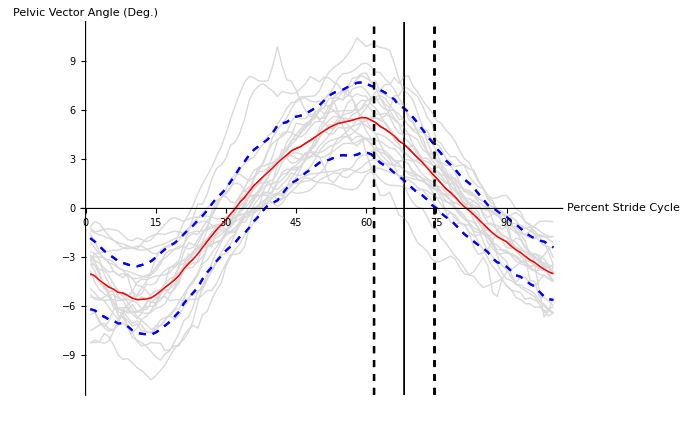

```mathematica
(*Need to add in start of swing phase line*)
(*IMPORT FRAME OF START OF SWING = absolute frame of start of swing phase minus start of limb cycle frame - this gives the position of the start of swing when only one limb cycle is shown*)

dataDirectory="YOUR DIRECTROY FOR EXPORTED STRIDE CYCLE EVENT DATA";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

StartofSwingFrameAnimal0Trial1=Flatten[Import["KM01_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal1Trial1=Flatten[Import["KM02_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal1Trial2=Flatten[Import["KM02_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal1Trial3=Flatten[Import["KM02_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal2Trial1=Flatten[Import["KM04_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal2Trial2=Flatten[Import["KM04_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal2Trial3=Flatten[Import["KM04_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal3Trial1=Flatten[Import["KM05_RUN_04_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal3Trial2=Flatten[Import["KM05_RUN_08_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal4Trial1=Flatten[Import["KM06_RUN_11_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal4Trial2=Flatten[Import["KM06_RUN_12_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal4Trial3=Flatten[Import["KM06_RUN_13_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal4Trial4=Flatten[Import["KM06_RUN_15_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal4Trial5=Flatten[Import["KM06_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal5Trial1=Flatten[Import["KM07_RUN_14_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal5Trial2=Flatten[Import["KM07_RUN_16_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal5Trial3=Flatten[Import["KM07_RUN_17_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal6Trial1=Flatten[Import["KM08_RUN_09_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal6Trial2=Flatten[Import["KM08_RUN_10_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal7Trial1=Flatten[Import["KM23_RUN_01_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal7Trial2=Flatten[Import["KM23_RUN_02_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal7Trial3=Flatten[Import["KM23_RUN_03_Start of Swing relative frame number.xlsx","Data"]];
StartofSwingFrameAnimal7Trial4=Flatten[Import["KM23_RUN_05_Start of Swing relative frame number.xlsx","Data"]];

(*********************************************************************)

(*Start of swing phase when time normalised*)

TNStartofSwingAnimal0Trial1=(StartofSwingFrameAnimal0Trial1/LengthAnimal0Trial1)*DesiredLengthofData;
TNStartofSwingAnimal1Trial1=(StartofSwingFrameAnimal1Trial1/LengthAnimal1Trial1)*DesiredLengthofData;
TNStartofSwingAnimal1Trial2=(StartofSwingFrameAnimal1Trial2/LengthAnimal1Trial2)*DesiredLengthofData;
TNStartofSwingAnimal1Trial3=(StartofSwingFrameAnimal1Trial3/LengthAnimal1Trial3)*DesiredLengthofData;
TNStartofSwingAnimal2Trial1=(StartofSwingFrameAnimal2Trial1/LengthAnimal2Trial1)*DesiredLengthofData;
TNStartofSwingAnimal2Trial2=(StartofSwingFrameAnimal2Trial2/LengthAnimal2Trial2)*DesiredLengthofData;
TNStartofSwingAnimal2Trial3=(StartofSwingFrameAnimal2Trial3/LengthAnimal2Trial3)*DesiredLengthofData;
TNStartofSwingAnimal4Trial1=(StartofSwingFrameAnimal4Trial1/LengthAnimal4Trial1)*DesiredLengthofData;
TNStartofSwingAnimal4Trial2=(StartofSwingFrameAnimal4Trial2/LengthAnimal4Trial2)*DesiredLengthofData;
TNStartofSwingAnimal4Trial3=(StartofSwingFrameAnimal4Trial3/LengthAnimal4Trial3)*DesiredLengthofData;
TNStartofSwingAnimal4Trial4=(StartofSwingFrameAnimal4Trial4/LengthAnimal4Trial4)*DesiredLengthofData;
TNStartofSwingAnimal4Trial5=(StartofSwingFrameAnimal4Trial5/LengthAnimal4Trial5)*DesiredLengthofData;
TNStartofSwingAnimal5Trial1=(StartofSwingFrameAnimal5Trial1/LengthAnimal5Trial1)*DesiredLengthofData;
TNStartofSwingAnimal5Trial2=(StartofSwingFrameAnimal5Trial2/LengthAnimal5Trial2)*DesiredLengthofData;
TNStartofSwingAnimal5Trial3=(StartofSwingFrameAnimal5Trial3/LengthAnimal5Trial3)*DesiredLengthofData;
TNStartofSwingAnimal6Trial1=(StartofSwingFrameAnimal6Trial1/LengthAnimal6Trial1)*DesiredLengthofData;
TNStartofSwingAnimal6Trial2=(StartofSwingFrameAnimal6Trial2/LengthAnimal6Trial2)*DesiredLengthofData;
TNStartofSwingAnimal7Trial1=(StartofSwingFrameAnimal7Trial1/LengthAnimal7Trial1)*DesiredLengthofData;
TNStartofSwingAnimal7Trial2=(StartofSwingFrameAnimal7Trial2/LengthAnimal7Trial2)*DesiredLengthofData;
TNStartofSwingAnimal7Trial3=(StartofSwingFrameAnimal7Trial3/LengthAnimal7Trial3)*DesiredLengthofData;
TNStartofSwingAnimal7Trial4=(StartofSwingFrameAnimal7Trial4/LengthAnimal7Trial4)*DesiredLengthofData;

(*********************************************************************)

(*Make table of start of swing frames*)

StartofSwingFrameAllTrials=Join[TNStartofSwingAnimal0Trial1,TNStartofSwingAnimal1Trial1,TNStartofSwingAnimal1Trial2,TNStartofSwingAnimal1Trial3,TNStartofSwingAnimal2Trial1,TNStartofSwingAnimal2Trial2,TNStartofSwingAnimal2Trial3,TNStartofSwingAnimal4Trial1,TNStartofSwingAnimal4Trial2,TNStartofSwingAnimal4Trial3,TNStartofSwingAnimal4Trial4,TNStartofSwingAnimal4Trial5,TNStartofSwingAnimal5Trial1,TNStartofSwingAnimal5Trial2,TNStartofSwingAnimal5Trial3,TNStartofSwingAnimal6Trial1,TNStartofSwingAnimal6Trial2,TNStartofSwingAnimal7Trial1,TNStartofSwingAnimal7Trial2,TNStartofSwingAnimal7Trial3,TNStartofSwingAnimal7Trial4];

(*********************************************************************)

(*Get mean and SD*)

MeanStartofSwing=Mean[StartofSwingFrameAllTrials];
SDStartofSwing=StandardDeviation[StartofSwingFrameAllTrials];

MeanPlusSDStartofSwing=MeanStartofSwing+SDStartofSwing;
MeanMinusSDStartofSwing=MeanStartofSwing-SDStartofSwing;

(*********************************************************************)

(*PLOT OF MEAN +/- SD PELVIC VECTOR ANGLE WITH START OF SWING PHASE LINES*)

(*Swing phase line mean +/- SD*)

MeanStartofSwingDatatoPlot={{MeanStartofSwing,100},{MeanStartofSwing,-100}};
MeanStartofSwingPlot=ListLinePlot[MeanStartofSwingDatatoPlot,PlotStyle->{Thick,Black}];

MeanPlusSDStartofSwingDatatoPlot={{MeanPlusSDStartofSwing,100},{MeanPlusSDStartofSwing,-100}};
MeanPlusSDStartofSwingPlot=ListLinePlot[MeanPlusSDStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanMinusSDStartofSwingDatatoPlot={{MeanMinusSDStartofSwing,100},{MeanMinusSDStartofSwing,-100}};
MeanMinusSDStartofSwingPlot=ListLinePlot[MeanMinusSDStartofSwingDatatoPlot,PlotStyle->{Dashed,Black}];

MeanSDStartofSwingPlot=Show[MeanStartofSwingPlot,MeanPlusSDStartofSwingPlot,MeanMinusSDStartofSwingPlot];

(*Plot mean +/- SD pelvic angle data with 1 eg. trial in grey*)

MeanPelvicAnglePlot=ListLinePlot[MeanPelvicAngleDataPoints,PlotStyle->{Thick,Red}];
PlusSDPelvicAnglePlot=ListLinePlot[MeanPlusSDPelvicAngleDataPoints,PlotStyle->{Dashed,Blue}];
MinusSDPelvicAnglePlot=ListLinePlot[MeanMinusSDPelvicAngleDataPoints,PlotStyle->{Dashed,Blue}];
RSAnimal3Trial1PlotforMeanSDPlot=ListLinePlot[RSAnimal3Trial1,PlotStyle->{Gray,Thick}];


MeanSDPelvicAnglePlot=Show[MeanPelvicAnglePlot,PlusSDPelvicAnglePlot,MinusSDPelvicAnglePlot,MeanSDStartofSwingPlot,PlotRange->{-11,11},AxesLabel->{"Percent Stride Cycle","Pelvic Vector Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,Medium],LabelStyle->Directive[Bold,Gray,FontFamily->"Calibri",FontSize->Large],AxesOrigin->{0,0},ImageSize->700];


(*Plot mean +/- SD pelvic angle data with swing phase line +/- SD with ALL trial in grey*)

MeanSDPelvicAnglePlotwithswingphaselines=Show[MeanSDPelvicAnglePlot,MeanSDStartofSwingPlot,AllRSAnimalsAllTrials,MeanSDPelvicAnglePlot]
```

```mathematica
AllPelvicAngle=Show[AllRSAnimalsAllTrials,MeanSDStartofSwingPlot,PlotRange->{-11,11},AxesLabel->{"Percent Stride Cycle","Pelvic Vector Angle (Deg.)"},Axes->True,AxesStyle->Directive[Gray,15],LabelStyle->Directive[{Bold,Gray,FontFamily->"Calibri"}],AxesOrigin->{0,0},ImageSize->700];
```

```mathematica
(*********************************************************************)

(*EXPORT*)

dataDirectory="YOUR DIRECTORY FOR EXPORTED FIGURES";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];


Export["Kinematics Paper - All Pelvic Vector Angle Plot.svg",AllPelvicAngle];
Export["Kinematics Paper - Mean plus.minus SD Pelvic Vector Angle Plot.svg",MeanSDPelvicAnglePlotwithswingphaselines];
Print["EXPORTED"]
```

EXPORTED

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Joint distance/hypothetical gain in stride length plots*)

dataDirectory="Amber\\Data\\Kinematics Paper - Exported data\\Joint distance travelled data";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

(*********************************************************************)

(*Import joint distance travelled data*)

(*Fixed body axis Model 1 - with pelvic rotation*)

(*Ankle*)
Animal0Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM01_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_01_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial3AnkleModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_11_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial3AnkleModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_12_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_04_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_08_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_11_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_12_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial3AnkleModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_13_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial4AnkleModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_15_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial5AnkleModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_16_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_14_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_16_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial3AnkleModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_17_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_09_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_10_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial1AnkleModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_01_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial2AnkleModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_02_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial3AnkleModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_03_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial4AnkleModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_05_Ankle distance travelled - Model 1 Fixed body axis.xlsx","Data"]];

(*Knee*)

Animal0Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM01_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_01_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial3KneeModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_11_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial3KneeModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_12_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_04_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_08_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_11_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_12_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial3KneeModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_13_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial4KneeModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_15_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial5KneeModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_16_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_14_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_16_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial3KneeModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_17_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_09_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_10_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial1KneeModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_01_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial2KneeModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_02_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial3KneeModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_03_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial4KneeModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_05_Knee distance travelled - Model 1 Fixed body axis.xlsx","Data"]];

(*TMT*)

Animal0Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM01_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_01_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal1Trial3TMTModel1DistanceTravelleddata=Flatten[Import["KM02_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_11_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal2Trial3TMTModel1DistanceTravelleddata=Flatten[Import["KM04_RUN_12_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_04_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal3Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM05_RUN_08_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_11_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_12_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial3TMTModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_13_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial4TMTModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_15_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal4Trial5TMTModel1DistanceTravelleddata=Flatten[Import["KM06_RUN_16_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_14_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_16_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal5Trial3TMTModel1DistanceTravelleddata=Flatten[Import["KM07_RUN_17_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_09_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal6Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM08_RUN_10_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial1TMTModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_01_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial2TMTModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_02_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial3TMTModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_03_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
Animal7Trial4TMTModel1DistanceTravelleddata=Flatten[Import["KM23_RUN_05_TMT distance travelled - Model 1 Fixed body axis.xlsx","Data"]];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Fixed body axis Model 1 - with pelvic rotation*)
(*1. Join data for each joint*)

(*Ankle*)
AllAnkleModel1DistanceTravelled=Join[{Animal0Trial1AnkleModel1DistanceTravelleddata[[1]],Animal1Trial1AnkleModel1DistanceTravelleddata[[1]],Animal1Trial2AnkleModel1DistanceTravelleddata[[1]],Animal1Trial3AnkleModel1DistanceTravelleddata[[1]],Animal2Trial1AnkleModel1DistanceTravelleddata[[1]],Animal2Trial2AnkleModel1DistanceTravelleddata[[1]],Animal2Trial3AnkleModel1DistanceTravelleddata[[1]],Animal3Trial1AnkleModel1DistanceTravelleddata[[1]],Animal3Trial2AnkleModel1DistanceTravelleddata[[1]],Animal4Trial1AnkleModel1DistanceTravelleddata[[1]],Animal4Trial2AnkleModel1DistanceTravelleddata[[1]],Animal4Trial3AnkleModel1DistanceTravelleddata[[1]],Animal4Trial4AnkleModel1DistanceTravelleddata[[1]],Animal4Trial5AnkleModel1DistanceTravelleddata[[1]],Animal5Trial1AnkleModel1DistanceTravelleddata[[1]],Animal5Trial2AnkleModel1DistanceTravelleddata[[1]],Animal5Trial3AnkleModel1DistanceTravelleddata[[1]],Animal6Trial1AnkleModel1DistanceTravelleddata[[1]],Animal6Trial2AnkleModel1DistanceTravelleddata[[1]],Animal7Trial1AnkleModel1DistanceTravelleddata[[1]],Animal7Trial2AnkleModel1DistanceTravelleddata[[1]],Animal7Trial3AnkleModel1DistanceTravelleddata[[1]],Animal7Trial4AnkleModel1DistanceTravelleddata[[1]]}];

(*Knee*)
AllKneeModel1DistanceTravelled=Join[{Animal0Trial1KneeModel1DistanceTravelleddata[[1]],Animal1Trial1KneeModel1DistanceTravelleddata[[1]],Animal1Trial2KneeModel1DistanceTravelleddata[[1]],Animal1Trial3KneeModel1DistanceTravelleddata[[1]],Animal2Trial1KneeModel1DistanceTravelleddata[[1]],Animal2Trial2KneeModel1DistanceTravelleddata[[1]],Animal2Trial3KneeModel1DistanceTravelleddata[[1]],Animal3Trial1KneeModel1DistanceTravelleddata[[1]],Animal3Trial2KneeModel1DistanceTravelleddata[[1]],Animal4Trial1KneeModel1DistanceTravelleddata[[1]],Animal4Trial2KneeModel1DistanceTravelleddata[[1]],Animal4Trial3KneeModel1DistanceTravelleddata[[1]],Animal4Trial4KneeModel1DistanceTravelleddata[[1]],Animal4Trial5KneeModel1DistanceTravelleddata[[1]],Animal5Trial1KneeModel1DistanceTravelleddata[[1]],Animal5Trial2KneeModel1DistanceTravelleddata[[1]],Animal5Trial3KneeModel1DistanceTravelleddata[[1]],Animal6Trial1KneeModel1DistanceTravelleddata[[1]],Animal6Trial2KneeModel1DistanceTravelleddata[[1]],Animal7Trial1KneeModel1DistanceTravelleddata[[1]],Animal7Trial2KneeModel1DistanceTravelleddata[[1]],Animal7Trial3KneeModel1DistanceTravelleddata[[1]],Animal7Trial4KneeModel1DistanceTravelleddata[[1]]}];

(*TMT*)
AllTMTModel1DistanceTravelled=Join[{Animal0Trial1TMTModel1DistanceTravelleddata[[1]],Animal1Trial1TMTModel1DistanceTravelleddata[[1]],Animal1Trial2TMTModel1DistanceTravelleddata[[1]],Animal1Trial3TMTModel1DistanceTravelleddata[[1]],Animal2Trial1TMTModel1DistanceTravelleddata[[1]],Animal2Trial2TMTModel1DistanceTravelleddata[[1]],Animal2Trial3TMTModel1DistanceTravelleddata[[1]],Animal3Trial1TMTModel1DistanceTravelleddata[[1]],Animal3Trial2TMTModel1DistanceTravelleddata[[1]],Animal4Trial1TMTModel1DistanceTravelleddata[[1]],Animal4Trial2TMTModel1DistanceTravelleddata[[1]],Animal4Trial3TMTModel1DistanceTravelleddata[[1]],Animal4Trial4TMTModel1DistanceTravelleddata[[1]],Animal4Trial5TMTModel1DistanceTravelleddata[[1]],Animal5Trial1TMTModel1DistanceTravelleddata[[1]],Animal5Trial2TMTModel1DistanceTravelleddata[[1]],Animal5Trial3TMTModel1DistanceTravelleddata[[1]],Animal6Trial1TMTModel1DistanceTravelleddata[[1]],Animal6Trial2TMTModel1DistanceTravelleddata[[1]],Animal7Trial1TMTModel1DistanceTravelleddata[[1]],Animal7Trial2TMTModel1DistanceTravelleddata[[1]],Animal7Trial3TMTModel1DistanceTravelleddata[[1]],Animal7Trial4TMTModel1DistanceTravelleddata[[1]]}];


(*2. Get average for each joint*)

(*Ankle*)
AVAnkleModel1DistanceTravelled=Mean[AllAnkleModel1DistanceTravelled];

(*Knee*)
AVKneeModel1DistanceTravelled=Mean[AllKneeModel1DistanceTravelled];

(*TMT*)
AVTMTModel1DistanceTravelled=Mean[AllTMTModel1DistanceTravelled];


(*3. Get SD for each joint*)

(*Ankle*)
SDAnkleModel1DistanceTravelled=StandardDeviation[AllAnkleModel1DistanceTravelled];

(*Knee*)
SDKneeModel1DistanceTravelled=StandardDeviation[AllKneeModel1DistanceTravelled];

(*TMT*)
SDTMTModel1DistanceTravelled=StandardDeviation[AllTMTModel1DistanceTravelled];


(*4. Mean +/- SD for each joint*)

(*Ankle*)
MeanPlusSDAnkleModel1DistanceTravelled=AVAnkleModel1DistanceTravelled+SDAnkleModel1DistanceTravelled;
MeanMinusSDAnkleModel1DistanceTravelled=AVAnkleModel1DistanceTravelled-SDAnkleModel1DistanceTravelled;

(*Knee*)
MeanPlusSDKneeModel1DistanceTravelled=AVKneeModel1DistanceTravelled+SDKneeModel1DistanceTravelled;
MeanMinusSDKneeModel1DistanceTravelled=AVKneeModel1DistanceTravelled-SDKneeModel1DistanceTravelled;

(*TMT*)
MeanPlusSDTMTModel1DistanceTravelled=AVTMTModel1DistanceTravelled+SDTMTModel1DistanceTravelled;
MeanMinusSDTMTModel1DistanceTravelled=AVTMTModel1DistanceTravelled-SDTMTModel1DistanceTravelled;
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Import joint distance travelled data*)
(*Fixed pelvic vector angle Model 2 - without pelvic rotation*)

(*Ankle*)
Animal0Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM01_RUN_02_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_01_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_02_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial3AnkleModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_09_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_09_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_11_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial3AnkleModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_12_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_04_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_08_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_11_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_12_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial3AnkleModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_13_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial4AnkleModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_15_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial5AnkleModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_16_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_14_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_16_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial3AnkleModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_17_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_09_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_10_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial1AnkleModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_01_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial2AnkleModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_02_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial3AnkleModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_03_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial4AnkleModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_05_Ankle distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];

(*Knee*)
Animal0Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM01_RUN_02_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_01_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_02_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial3KneeModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_09_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_09_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_11_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial3KneeModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_12_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_04_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_08_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_11_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_12_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial3KneeModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_13_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial4KneeModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_15_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial5KneeModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_16_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_14_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_16_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial3KneeModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_17_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_09_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_10_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial1KneeModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_01_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial2KneeModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_02_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial3KneeModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_03_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial4KneeModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_05_Knee distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];

(*TMT*)
Animal0Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM01_RUN_02_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_01_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_02_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal1Trial3TMTModel2DistanceTravelleddata=Flatten[Import["KM02_RUN_09_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_09_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_11_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal2Trial3TMTModel2DistanceTravelleddata=Flatten[Import["KM04_RUN_12_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_04_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal3Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM05_RUN_08_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_11_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_12_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial3TMTModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_13_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial4TMTModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_15_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal4Trial5TMTModel2DistanceTravelleddata=Flatten[Import["KM06_RUN_16_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_14_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_16_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal5Trial3TMTModel2DistanceTravelleddata=Flatten[Import["KM07_RUN_17_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_09_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal6Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM08_RUN_10_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial1TMTModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_01_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial2TMTModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_02_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];Animal7Trial3TMTModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_03_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
Animal7Trial4TMTModel2DistanceTravelleddata=Flatten[Import["KM23_RUN_05_TMT distance travelled - Model 2 Fixed pelvic vector.xlsx","Data"]];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Fixed pelvic vector angle Model 2 - without pelvic rotation*)
(*1. Join data for each joint*)

(*Ankle*)
AllAnkleModel2DistanceTravelled=Join[{Animal0Trial1AnkleModel2DistanceTravelleddata[[1]],Animal1Trial1AnkleModel2DistanceTravelleddata[[1]],Animal1Trial2AnkleModel2DistanceTravelleddata[[1]],Animal1Trial3AnkleModel2DistanceTravelleddata[[1]],Animal2Trial1AnkleModel2DistanceTravelleddata[[1]],Animal2Trial2AnkleModel2DistanceTravelleddata[[1]],Animal2Trial3AnkleModel2DistanceTravelleddata[[1]],Animal3Trial1AnkleModel2DistanceTravelleddata[[1]],Animal3Trial2AnkleModel2DistanceTravelleddata[[1]],Animal4Trial1AnkleModel2DistanceTravelleddata[[1]],Animal4Trial2AnkleModel2DistanceTravelleddata[[1]],Animal4Trial3AnkleModel2DistanceTravelleddata[[1]],Animal4Trial4AnkleModel2DistanceTravelleddata[[1]],Animal4Trial5AnkleModel2DistanceTravelleddata[[1]],Animal5Trial1AnkleModel2DistanceTravelleddata[[1]],Animal5Trial2AnkleModel2DistanceTravelleddata[[1]],Animal5Trial3AnkleModel2DistanceTravelleddata[[1]],Animal6Trial1AnkleModel2DistanceTravelleddata[[1]],Animal6Trial2AnkleModel2DistanceTravelleddata[[1]],Animal7Trial1AnkleModel2DistanceTravelleddata[[1]],Animal7Trial2AnkleModel2DistanceTravelleddata[[1]],Animal7Trial3AnkleModel2DistanceTravelleddata[[1]],Animal7Trial4AnkleModel2DistanceTravelleddata[[1]]}];

(*Knee*)
AllKneeModel2DistanceTravelled=Join[{Animal0Trial1KneeModel2DistanceTravelleddata[[1]],Animal1Trial1KneeModel2DistanceTravelleddata[[1]],Animal1Trial2KneeModel2DistanceTravelleddata[[1]],Animal1Trial3KneeModel2DistanceTravelleddata[[1]],Animal2Trial1KneeModel2DistanceTravelleddata[[1]],Animal2Trial2KneeModel2DistanceTravelleddata[[1]],Animal2Trial3KneeModel2DistanceTravelleddata[[1]],Animal3Trial1KneeModel2DistanceTravelleddata[[1]],Animal3Trial2KneeModel2DistanceTravelleddata[[1]],Animal4Trial1KneeModel2DistanceTravelleddata[[1]],Animal4Trial2KneeModel2DistanceTravelleddata[[1]],Animal4Trial3KneeModel2DistanceTravelleddata[[1]],Animal4Trial4KneeModel2DistanceTravelleddata[[1]],Animal4Trial5KneeModel2DistanceTravelleddata[[1]],Animal5Trial1KneeModel2DistanceTravelleddata[[1]],Animal5Trial2KneeModel2DistanceTravelleddata[[1]],Animal5Trial3KneeModel2DistanceTravelleddata[[1]],Animal6Trial1KneeModel2DistanceTravelleddata[[1]],Animal6Trial2KneeModel2DistanceTravelleddata[[1]],Animal7Trial1KneeModel2DistanceTravelleddata[[1]],Animal7Trial2KneeModel2DistanceTravelleddata[[1]],Animal7Trial3KneeModel2DistanceTravelleddata[[1]],Animal7Trial4KneeModel2DistanceTravelleddata[[1]]}];

(*TMT*)
AllTMTModel2DistanceTravelled=Join[{Animal0Trial1TMTModel2DistanceTravelleddata[[1]],Animal1Trial1TMTModel2DistanceTravelleddata[[1]],Animal1Trial2TMTModel2DistanceTravelleddata[[1]],Animal1Trial3TMTModel2DistanceTravelleddata[[1]],Animal2Trial1TMTModel2DistanceTravelleddata[[1]],Animal2Trial2TMTModel2DistanceTravelleddata[[1]],Animal2Trial3TMTModel2DistanceTravelleddata[[1]],Animal3Trial1TMTModel2DistanceTravelleddata[[1]],Animal3Trial2TMTModel2DistanceTravelleddata[[1]],Animal4Trial1TMTModel2DistanceTravelleddata[[1]],Animal4Trial2TMTModel2DistanceTravelleddata[[1]],Animal4Trial3TMTModel2DistanceTravelleddata[[1]],Animal4Trial4TMTModel2DistanceTravelleddata[[1]],Animal4Trial5TMTModel2DistanceTravelleddata[[1]],Animal5Trial1TMTModel2DistanceTravelleddata[[1]],Animal5Trial2TMTModel2DistanceTravelleddata[[1]],Animal5Trial3TMTModel2DistanceTravelleddata[[1]],Animal6Trial1TMTModel2DistanceTravelleddata[[1]],Animal6Trial2TMTModel2DistanceTravelleddata[[1]],Animal7Trial1TMTModel2DistanceTravelleddata[[1]],Animal7Trial2TMTModel2DistanceTravelleddata[[1]],Animal7Trial3TMTModel2DistanceTravelleddata[[1]],Animal7Trial4TMTModel2DistanceTravelleddata[[1]]}];


(*2. Get average for each joint*)

(*Ankle*)
AVAnkleModel2DistanceTravelled=Mean[AllAnkleModel2DistanceTravelled];

(*Knee*)
AVKneeModel2DistanceTravelled=Mean[AllKneeModel2DistanceTravelled];

(*TMT*)
AVTMTModel2DistanceTravelled=Mean[AllTMTModel2DistanceTravelled];


(*3. Get SD for each joint*)

(*Ankle*)
SDAnkleModel2DistanceTravelled=StandardDeviation[AllAnkleModel2DistanceTravelled];

(*Knee*)
SDKneeModel2DistanceTravelled=StandardDeviation[AllKneeModel2DistanceTravelled];

(*TMT*)
SDTMTModel2DistanceTravelled=StandardDeviation[AllTMTModel2DistanceTravelled];


(*4. Mean +/- SD for each joint*)

(*Ankle*)
MeanPlusSDAnkleModel2DistanceTravelled=AVAnkleModel2DistanceTravelled+SDAnkleModel2DistanceTravelled;
MeanMinusSDAnkleModel2DistanceTravelled=AVAnkleModel2DistanceTravelled-SDAnkleModel2DistanceTravelled;

(*Knee*)
MeanPlusSDKneeModel2DistanceTravelled=AVKneeModel2DistanceTravelled+SDKneeModel2DistanceTravelled;
MeanMinusSDKneeModel2DistanceTravelled=AVKneeModel2DistanceTravelled-SDKneeModel2DistanceTravelled;

(*TMT*)
MeanPlusSDTMTModel2DistanceTravelled=AVTMTModel2DistanceTravelled+SDTMTModel2DistanceTravelled;
MeanMinusSDTMTModel2DistanceTravelled=AVTMTModel2DistanceTravelled-SDTMTModel2DistanceTravelled;
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Import hypothetical gain in distance data*)
(*Difference in joint distances travelled - Hypothetical gain*)

(*Ankle*)
Animal0Trial1AnkleHypotheticalGaindata=Flatten[Import["KM01_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal1Trial1AnkleHypotheticalGaindata=Flatten[Import["KM02_RUN_01_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal1Trial2AnkleHypotheticalGaindata=Flatten[Import["KM02_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal1Trial3AnkleHypotheticalGaindata=Flatten[Import["KM02_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal2Trial1AnkleHypotheticalGaindata=Flatten[Import["KM04_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal2Trial2AnkleHypotheticalGaindata=Flatten[Import["KM04_RUN_11_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal2Trial3AnkleHypotheticalGaindata=Flatten[Import["KM04_RUN_12_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal3Trial1AnkleHypotheticalGaindata=Flatten[Import["KM05_RUN_04_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal3Trial2AnkleHypotheticalGaindata=Flatten[Import["KM05_RUN_08_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal4Trial1AnkleHypotheticalGaindata=Flatten[Import["KM06_RUN_11_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal4Trial2AnkleHypotheticalGaindata=Flatten[Import["KM06_RUN_12_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal4Trial3AnkleHypotheticalGaindata=Flatten[Import["KM06_RUN_13_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal4Trial4AnkleHypotheticalGaindata=Flatten[Import["KM06_RUN_15_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal4Trial5AnkleHypotheticalGaindata=Flatten[Import["KM06_RUN_16_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal5Trial1AnkleHypotheticalGaindata=Flatten[Import["KM07_RUN_14_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal5Trial2AnkleHypotheticalGaindata=Flatten[Import["KM07_RUN_16_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal5Trial3AnkleHypotheticalGaindata=Flatten[Import["KM07_RUN_17_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal6Trial1AnkleHypotheticalGaindata=Flatten[Import["KM08_RUN_09_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal6Trial2AnkleHypotheticalGaindata=Flatten[Import["KM08_RUN_10_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal7Trial1AnkleHypotheticalGaindata=Flatten[Import["KM23_RUN_01_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal7Trial2AnkleHypotheticalGaindata=Flatten[Import["KM23_RUN_02_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal7Trial3AnkleHypotheticalGaindata=Flatten[Import["KM23_RUN_03_Ankle hypothetical gain in distance.xlsx","Data"]];
Animal7Trial4AnkleHypotheticalGaindata=Flatten[Import["KM23_RUN_05_Ankle hypothetical gain in distance.xlsx","Data"]];

(*Knee*)
Animal0Trial1KneeHypotheticalGaindata=Flatten[Import["KM01_RUN_02_Knee hypothetical gain in distance.xlsx","Data"]];
Animal1Trial1KneeHypotheticalGaindata=Flatten[Import["KM02_RUN_01_Knee hypothetical gain in distance.xlsx","Data"]];
Animal1Trial2KneeHypotheticalGaindata=Flatten[Import["KM02_RUN_02_Knee hypothetical gain in distance.xlsx","Data"]];
Animal1Trial3KneeHypotheticalGaindata=Flatten[Import["KM02_RUN_09_Knee hypothetical gain in distance.xlsx","Data"]];
Animal2Trial1KneeHypotheticalGaindata=Flatten[Import["KM04_RUN_09_Knee hypothetical gain in distance.xlsx","Data"]];
Animal2Trial2KneeHypotheticalGaindata=Flatten[Import["KM04_RUN_11_Knee hypothetical gain in distance.xlsx","Data"]];
Animal2Trial3KneeHypotheticalGaindata=Flatten[Import["KM04_RUN_12_Knee hypothetical gain in distance.xlsx","Data"]];
Animal3Trial1KneeHypotheticalGaindata=Flatten[Import["KM05_RUN_04_Knee hypothetical gain in distance.xlsx","Data"]];
Animal3Trial2KneeHypotheticalGaindata=Flatten[Import["KM05_RUN_08_Knee hypothetical gain in distance.xlsx","Data"]];
Animal4Trial1KneeHypotheticalGaindata=Flatten[Import["KM06_RUN_11_Knee hypothetical gain in distance.xlsx","Data"]];
Animal4Trial2KneeHypotheticalGaindata=Flatten[Import["KM06_RUN_12_Knee hypothetical gain in distance.xlsx","Data"]];
Animal4Trial3KneeHypotheticalGaindata=Flatten[Import["KM06_RUN_13_Knee hypothetical gain in distance.xlsx","Data"]];
Animal4Trial4KneeHypotheticalGaindata=Flatten[Import["KM06_RUN_15_Knee hypothetical gain in distance.xlsx","Data"]];
Animal4Trial5KneeHypotheticalGaindata=Flatten[Import["KM06_RUN_16_Knee hypothetical gain in distance.xlsx","Data"]];
Animal5Trial1KneeHypotheticalGaindata=Flatten[Import["KM07_RUN_14_Knee hypothetical gain in distance.xlsx","Data"]];
Animal5Trial2KneeHypotheticalGaindata=Flatten[Import["KM07_RUN_16_Knee hypothetical gain in distance.xlsx","Data"]];
Animal5Trial3KneeHypotheticalGaindata=Flatten[Import["KM07_RUN_17_Knee hypothetical gain in distance.xlsx","Data"]];
Animal6Trial1KneeHypotheticalGaindata=Flatten[Import["KM08_RUN_09_Knee hypothetical gain in distance.xlsx","Data"]];
Animal6Trial2KneeHypotheticalGaindata=Flatten[Import["KM08_RUN_10_Knee hypothetical gain in distance.xlsx","Data"]];
Animal7Trial1KneeHypotheticalGaindata=Flatten[Import["KM23_RUN_01_Knee hypothetical gain in distance.xlsx","Data"]];
Animal7Trial2KneeHypotheticalGaindata=Flatten[Import["KM23_RUN_02_Knee hypothetical gain in distance.xlsx","Data"]];
Animal7Trial3KneeHypotheticalGaindata=Flatten[Import["KM23_RUN_03_Knee hypothetical gain in distance.xlsx","Data"]];
Animal7Trial4KneeHypotheticalGaindata=Flatten[Import["KM23_RUN_05_Knee hypothetical gain in distance.xlsx","Data"]];

(*TMT*)
Animal0Trial1TMTHypotheticalGaindata=Flatten[Import["KM01_RUN_02_TMT hypothetical gain in distance.xlsx","Data"]];
Animal1Trial1TMTHypotheticalGaindata=Flatten[Import["KM02_RUN_01_TMT hypothetical gain in distance.xlsx","Data"]];
Animal1Trial2TMTHypotheticalGaindata=Flatten[Import["KM02_RUN_02_TMT hypothetical gain in distance.xlsx","Data"]];
Animal1Trial3TMTHypotheticalGaindata=Flatten[Import["KM02_RUN_09_TMT hypothetical gain in distance.xlsx","Data"]];
Animal2Trial1TMTHypotheticalGaindata=Flatten[Import["KM04_RUN_09_TMT hypothetical gain in distance.xlsx","Data"]];
Animal2Trial2TMTHypotheticalGaindata=Flatten[Import["KM04_RUN_11_TMT hypothetical gain in distance.xlsx","Data"]];
Animal2Trial3TMTHypotheticalGaindata=Flatten[Import["KM04_RUN_12_TMT hypothetical gain in distance.xlsx","Data"]];
Animal3Trial1TMTHypotheticalGaindata=Flatten[Import["KM05_RUN_04_TMT hypothetical gain in distance.xlsx","Data"]];
Animal3Trial2TMTHypotheticalGaindata=Flatten[Import["KM05_RUN_08_TMT hypothetical gain in distance.xlsx","Data"]];
Animal4Trial1TMTHypotheticalGaindata=Flatten[Import["KM06_RUN_11_TMT hypothetical gain in distance.xlsx","Data"]];
Animal4Trial2TMTHypotheticalGaindata=Flatten[Import["KM06_RUN_12_TMT hypothetical gain in distance.xlsx","Data"]];
Animal4Trial3TMTHypotheticalGaindata=Flatten[Import["KM06_RUN_13_TMT hypothetical gain in distance.xlsx","Data"]];
Animal4Trial4TMTHypotheticalGaindata=Flatten[Import["KM06_RUN_15_TMT hypothetical gain in distance.xlsx","Data"]];
Animal4Trial5TMTHypotheticalGaindata=Flatten[Import["KM06_RUN_16_TMT hypothetical gain in distance.xlsx","Data"]];
Animal5Trial1TMTHypotheticalGaindata=Flatten[Import["KM07_RUN_14_TMT hypothetical gain in distance.xlsx","Data"]];
Animal5Trial2TMTHypotheticalGaindata=Flatten[Import["KM07_RUN_16_TMT hypothetical gain in distance.xlsx","Data"]];
Animal5Trial3TMTHypotheticalGaindata=Flatten[Import["KM07_RUN_17_TMT hypothetical gain in distance.xlsx","Data"]];
Animal6Trial1TMTHypotheticalGaindata=Flatten[Import["KM08_RUN_09_TMT hypothetical gain in distance.xlsx","Data"]];
Animal6Trial2TMTHypotheticalGaindata=Flatten[Import["KM08_RUN_10_TMT hypothetical gain in distance.xlsx","Data"]];
Animal7Trial1TMTHypotheticalGaindata=Flatten[Import["KM23_RUN_01_TMT hypothetical gain in distance.xlsx","Data"]];
Animal7Trial2TMTHypotheticalGaindata=Flatten[Import["KM23_RUN_02_TMT hypothetical gain in distance.xlsx","Data"]];
Animal7Trial3TMTHypotheticalGaindata=Flatten[Import["KM23_RUN_03_TMT hypothetical gain in distance.xlsx","Data"]];
Animal7Trial4TMTHypotheticalGaindata=Flatten[Import["KM23_RUN_05_TMT hypothetical gain in distance.xlsx","Data"]];
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

```mathematica
(*Difference in joint distances travelled - Hypothetical gain*)
(*1. Join data for each joint*)

(*Ankle*)
AllAnkleHypotheticalGain=Join[{Animal0Trial1AnkleHypotheticalGaindata[[1]],Animal1Trial1AnkleHypotheticalGaindata[[1]],Animal1Trial2AnkleHypotheticalGaindata[[1]],Animal1Trial3AnkleHypotheticalGaindata[[1]],Animal2Trial1AnkleHypotheticalGaindata[[1]],Animal2Trial2AnkleHypotheticalGaindata[[1]],Animal2Trial3AnkleHypotheticalGaindata[[1]],Animal3Trial1AnkleHypotheticalGaindata[[1]],Animal3Trial2AnkleHypotheticalGaindata[[1]],Animal4Trial1AnkleHypotheticalGaindata[[1]],Animal4Trial2AnkleHypotheticalGaindata[[1]],Animal4Trial3AnkleHypotheticalGaindata[[1]],Animal4Trial4AnkleHypotheticalGaindata[[1]],Animal4Trial5AnkleHypotheticalGaindata[[1]],Animal5Trial1AnkleHypotheticalGaindata[[1]],Animal5Trial2AnkleHypotheticalGaindata[[1]],Animal5Trial3AnkleHypotheticalGaindata[[1]],Animal6Trial1AnkleHypotheticalGaindata[[1]],Animal6Trial2AnkleHypotheticalGaindata[[1]],Animal7Trial1AnkleHypotheticalGaindata[[1]],Animal7Trial2AnkleHypotheticalGaindata[[1]],Animal7Trial3AnkleHypotheticalGaindata[[1]],Animal7Trial4AnkleHypotheticalGaindata[[1]]}];

(*Knee*)
AllKneeHypotheticalGain=Join[{Animal0Trial1KneeHypotheticalGaindata[[1]],Animal1Trial1KneeHypotheticalGaindata[[1]],Animal1Trial2KneeHypotheticalGaindata[[1]],Animal1Trial3KneeHypotheticalGaindata[[1]],Animal2Trial1KneeHypotheticalGaindata[[1]],Animal2Trial2KneeHypotheticalGaindata[[1]],Animal2Trial3KneeHypotheticalGaindata[[1]],Animal3Trial1KneeHypotheticalGaindata[[1]],Animal3Trial2KneeHypotheticalGaindata[[1]],Animal4Trial1KneeHypotheticalGaindata[[1]],Animal4Trial2KneeHypotheticalGaindata[[1]],Animal4Trial3KneeHypotheticalGaindata[[1]],Animal4Trial4KneeHypotheticalGaindata[[1]],Animal4Trial5KneeHypotheticalGaindata[[1]],Animal5Trial1KneeHypotheticalGaindata[[1]],Animal5Trial2KneeHypotheticalGaindata[[1]],Animal5Trial3KneeHypotheticalGaindata[[1]],Animal6Trial1KneeHypotheticalGaindata[[1]],Animal6Trial2KneeHypotheticalGaindata[[1]],Animal7Trial1KneeHypotheticalGaindata[[1]],Animal7Trial2KneeHypotheticalGaindata[[1]],Animal7Trial3KneeHypotheticalGaindata[[1]],Animal7Trial4KneeHypotheticalGaindata[[1]]}];


(*TMT*)
AllTMTHypotheticalGain=Join[{Animal0Trial1TMTHypotheticalGaindata[[1]],Animal1Trial1TMTHypotheticalGaindata[[1]],Animal1Trial2TMTHypotheticalGaindata[[1]],Animal1Trial3TMTHypotheticalGaindata[[1]],Animal2Trial1TMTHypotheticalGaindata[[1]],Animal2Trial2TMTHypotheticalGaindata[[1]],Animal2Trial3TMTHypotheticalGaindata[[1]],Animal3Trial1TMTHypotheticalGaindata[[1]],Animal3Trial2TMTHypotheticalGaindata[[1]],Animal4Trial1TMTHypotheticalGaindata[[1]],Animal4Trial2TMTHypotheticalGaindata[[1]],Animal4Trial3TMTHypotheticalGaindata[[1]],Animal4Trial4TMTHypotheticalGaindata[[1]],Animal4Trial5TMTHypotheticalGaindata[[1]],Animal5Trial1TMTHypotheticalGaindata[[1]],Animal5Trial2TMTHypotheticalGaindata[[1]],Animal5Trial3TMTHypotheticalGaindata[[1]],Animal6Trial1TMTHypotheticalGaindata[[1]],Animal6Trial2TMTHypotheticalGaindata[[1]],Animal7Trial1TMTHypotheticalGaindata[[1]],Animal7Trial2TMTHypotheticalGaindata[[1]],Animal7Trial3TMTHypotheticalGaindata[[1]],Animal7Trial4TMTHypotheticalGaindata[[1]]}];



(*2. Get average hypothetical gain for each joint*)

(*Ankle*)
AVAnkleHypotheticalGain=Mean[AllAnkleHypotheticalGain];

(*Knee*)
AVKneeHypotheticalGain=Mean[AllKneeHypotheticalGain];

(*TMT*)
AVTMTHypotheticalGain=Mean[AllTMTHypotheticalGain];


(*3. Get SD for each joint*)

(*Ankle*)
SDAnkleHypotheticalGain=StandardDeviation[AllAnkleHypotheticalGain];

(*Knee*)
SDKneeHypotheticalGain=StandardDeviation[AllKneeHypotheticalGain];

(*TMT*)
SDTMTHypotheticalGain=StandardDeviation[AllTMTHypotheticalGain];


(*4. Mean +/- SD for each joint*)

(*Ankle*)
MeanPlusSDAnkleHypotheticalGain=AVAnkleHypotheticalGain+SDAnkleHypotheticalGain;
MeanMinusSDAnkleHypotheticalGain=AVAnkleHypotheticalGain-SDAnkleHypotheticalGain;

(*Knee*)
MeanPlusSDKneeHypotheticalGain=AVKneeHypotheticalGain+SDKneeHypotheticalGain;
MeanMinusSDKneeHypotheticalGain=AVKneeHypotheticalGain-SDKneeHypotheticalGain;

(*TMT*)
MeanPlusSDTMTHypotheticalGain=AVTMTHypotheticalGain+SDTMTHypotheticalGain;
MeanMinusSDTMTHypotheticalGain=AVTMTHypotheticalGain-SDTMTHypotheticalGain;
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

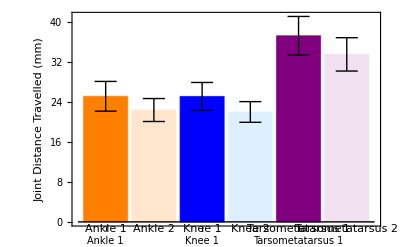

```mathematica
(*Produce bar charts*)

(*Create SD error bar function*)

SDErrorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=
Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];
{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4(3x0+x1),y1+error},{1/4(x0+3x1),y1+error}},{{1/4(3x0+x1),y1-error},{1/4(x0+3x1),y1-error}}}]}}]


(*Create chart data*)

(*Model 1 and 2*)

(*Model 1*)
MeanModel1DistanceTravelledChartData=Join[{AVAnkleModel1DistanceTravelled,AVKneeModel1DistanceTravelled,AVTMTModel1DistanceTravelled}];
SDModel1DistanceTravelledChartData=Join[{SDAnkleModel1DistanceTravelled,SDKneeModel1DistanceTravelled,SDTMTModel1DistanceTravelled}];

MeanandSDModel1DistanceTravelledChartData=Table[MeanModel1DistanceTravelledChartData[[i]]->SDModel1DistanceTravelledChartData[[i]],{i,1,Length[MeanModel1DistanceTravelledChartData]}];

(*Model 2*)
MeanModel2DistanceTravelledChartData=Join[{AVAnkleModel2DistanceTravelled,AVKneeModel2DistanceTravelled,AVTMTModel2DistanceTravelled}];
SDModel2DistanceTravelledChartData=Join[{SDAnkleModel2DistanceTravelled,SDKneeModel2DistanceTravelled,SDTMTModel2DistanceTravelled}];

MeanandSDModel2DistanceTravelledChartData=Table[MeanModel2DistanceTravelledChartData[[i]]->SDModel2DistanceTravelledChartData[[i]],{i,1,Length[MeanModel2DistanceTravelledChartData]}];


(*Model 1 and 2 data threaded*)
MeanandSDModel1and2DistanceTravelledChartData=Flatten[Thread[{MeanandSDModel1DistanceTravelledChartData,MeanandSDModel2DistanceTravelledChartData}]];

(*Set chart settings*)
barlabels={"Ankle 1","Ankle 2","Knee 1","Knee 2","Tarsometatarsus 1","Tarsometatarsus 2"};
axislabel={None,Style["Joint Distance Travelled (mm)",12 ,FontFamily->"Calibri"]};
barstyle={Orange,LightOrange,Blue,LightBlue,Purple,LightPurple};


(*Plot Chart with SD error bars*)
MeanModel1DistanceTravelledChartPlot=BarChart[MeanandSDModel1and2DistanceTravelledChartData,ChartElementFunction->SDErrorBar["Rectangle"],ChartLabels->barlabels,Frame->Left,FrameLabel->axislabel,ChartStyle->barstyle]
```

```mathematica
(*********************************************************************)
(*********************************************************************)
```

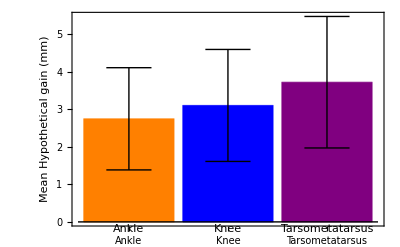

```mathematica
(*Hypothetical gain*)
MeanHypotheticalGainChartData=Join[{AVAnkleHypotheticalGain,AVKneeHypotheticalGain,AVTMTHypotheticalGain}];
SDHypotheticalGainChartData=Join[{SDAnkleHypotheticalGain,SDKneeHypotheticalGain,SDTMTHypotheticalGain}];

MeanandSDHypotheticalGainChartData=Table[MeanHypotheticalGainChartData[[i]]->SDHypotheticalGainChartData[[i]],{i,1,Length[MeanHypotheticalGainChartData]}];


(*Set chart settings*)
barlabels={"Ankle","Knee","Tarsometatarsus"};
axislabel={None,Style["Mean Hypothetical gain (mm)",12 ,FontFamily->"Calibri"]};
barstyle={Orange,Blue,Purple};


(*Plot Chart with SD error bars*)
MeanHypotheticalGainChartPlot= BarChart[MeanandSDHypotheticalGainChartData,ChartElementFunction->SDErrorBar["Rectangle"],ChartLabels->barlabels,Frame->Left,FrameLabel->axislabel,ChartStyle->barstyle]
```

```mathematica
(*Export Bar Charts*)

dataDirectory="Amber\\MM Code\\CHAPTER 1\\Kinematics Paper - Code and Images\\Kinematics Paper - Figures";

setpathDataWin=StringJoin[frogworkpath,dataDirectory];(*windows formatted path as string*)
splitpath=FileNameSplit[setpathDataWin,OperatingSystem->"Windows"(*change to MacOSX if necessary*)];
setpathData=FileNameJoin[splitpath,OperatingSystem->os];
SetDirectory[setpathData];

Export["Kinematics Papaer - Joint Distance Travelled Bar Chart.svg",MeanModel1DistanceTravelledChartPlot];
Export["Kinematics Papaer - Mean Hypothetical Gain Bar Chart.svg",MeanHypotheticalGainChartPlot];

Print["EXPORTED"]
```

EXPORTED